```mathematica
Predicting Bitcoin Bubbles
```

## References

- Transaction Dynamics of Blockchain and Predictable Bitcoin Bubbles. - https://polybox.ethz.ch/index.php/s/LzLmTZXzqF8rCAs

- Are Bitcoin Bubbles Predictable? Combining a Generalized Metcalfe’s Law and the LPPLS Model. - https://arxiv.org/pdf/1803.05663.pdf

- Metcalfe's law.

## Resources

- Bitcoin active addresses: bitinfocharts.com.

- Bitcoin market capitalization: bitinfocharts.com.

- Bitcoin hourly price: Bitcoin historical data - kaggle.com.

- Bitcoin circulating supply: https://www.blockchain.com/charts/total-bitcoins.

## In This Notebook

LPPLS model implementation (2018 ed.).

```mathematica
base=DirectoryName[NotebookFileName[]];
firstPrice="2012-01-01"
lastPrice="2021-03-31"
```

2012-01-01

2021-03-31

```mathematica
(* Compute Recent Log market cap data: *)
(* Prices list. Pre-processed for performance: *)
hourlyPricesList = Import[base<>"Bitcoin_price-hourly-"<>StringDelete[firstPrice, "-"]<>"-"<>StringDelete[lastPrice, "-"]<>".csv"]
```

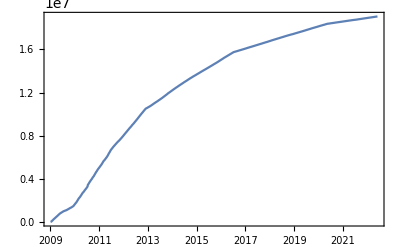

```mathematica
(* Convert to market capitalization, using circulating supply data, from blockchain.info *)
(* Load circulating supply data *)
supply = Import[base<>"Bitcoin_circulating_supply-"<>StringDelete[firstPrice, "-"]<>"-"<>StringDelete[lastPrice, "-"]<>".csv", HeaderLines->1];
DateListPlot[supply]
```

```mathematica
(* Convert to Unix timestamp: *)
supplyTimestamps = {UnixTime[ToString[#[[1]]]], #[[2]]}&/@supply;
```

```mathematica
(* Create an interpolating function from it *)
supplyFunction=Interpolation[supplyTimestamps]
```

InterpolatingFunction[…]

```mathematica
{supplyFunction[hourlyPricesList[[1]][[1]]], supplyFunction[hourlyPricesList[[-1]][[1]]]}
```

{7.99789×10^6,1.86692×10^7}

```mathematica
(* Generate hourly market capitalization data *)
hourlyMarketCap={#[[1]], #[[2]]*supplyFunction[#[[1]]]}&/@hourlyPricesList
```

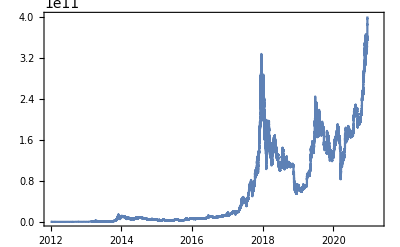

```mathematica
DateListPlot[hourlyMarketCap, DateFunction:> (FromUnixTime[#]&)]
```

```mathematica
(* Use the Log Market Cap *)
logMarketCap= {#[[1]], Log[#[[2]]]}&/@hourlyMarketCap
```

```mathematica
(* Appendix 5.1. Example: Analyze / predict the 2015 / 2018 bubble turning point: *)
(* Generalized to multiple bubbles *)
bubblesDate={{"2015-01-01", "2017-10-18"}, {"2019-11-25", "2021-02-13"}} (* From 2015 / ~2020 to 2 months before the turning point *)
```

{{2015-01-01,2017-10-18},{2019-11-25,2021-02-13}}

```mathematica
n=Length[bubblesDate]
```

2

```mathematica
(* Timestamp indexes: *)
bubblesTimestampIndex={UnixTime[#[[1]]], UnixTime[#[[2]]]}&/@bubblesDate
```

{{1420066800,1508281200},{1574636400,1613170800}}

```mathematica
bubblesDays=(#[[2]]-#[[1]])/86400&/@bubblesTimestampIndex
```

{1021,446}

```mathematica
bubbles=Table[Select[logMarketCap,bubblesTimestampIndex[[i]][[1]]≤#[[1]]≤ bubblesTimestampIndex[[i]][[2]]&], {i, n}];
#[[1]]&/@bubbles
```

{{1420066800,22.1981},{1574636400,25.5582}}

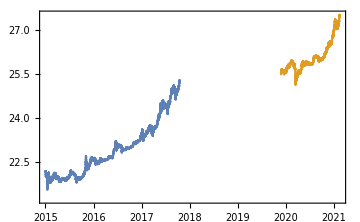

```mathematica
DateListPlot[bubbles, ImageSize->Medium, DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically *)
scaleH[data_]:= Module[{peaks, first},
(* Scale bubbles horizontally (0-1) (set 1 at the true peaks) *)
peaks=MaximalBy[data, Last][[1]];
first = data[[1]];
{(#[[1]]-first[[1]])/(peaks[[1]]-first[[1]]),#[[2]]}&/@data
]
```

```mathematica
scaleV[data_]:= Module[{min, max},
(* Rescale vertically *)
min=Min[Last /@data];
max=Max[Last /@data];
{#[[1]],(#[[2]]-min)/(max-min)}&/@data
]
```

```mathematica
bubblesScaled=scaleV[scaleH[#]]&/@ bubbles//N;
#[[-1]]&/@bubblesScaled
```

{{1.00282,0.989321},{1.00215,0.992478}}

```mathematica
Length/@bubblesScaled
```

{24398,10701}

```mathematica
(* LPPLS model over the scaled bubbles: *)
(* Step 1. Identify initial error model: *)
(* 1.a Fit the log market cap with a flexible nonparametric curve. *)
```

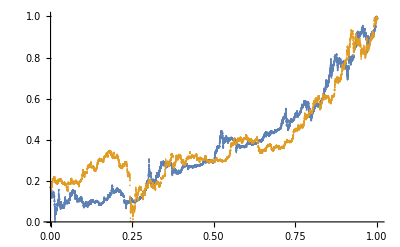

```mathematica
ListPlot[bubblesScaled]
```

```mathematica
(* 1.b Set up cross validation loop: *)
bandwidthSeq=Range[3, 10, 1]
```

{3,4,5,6,7,8,9,10}

```mathematica
k=10;
```

```mathematica
folds = RandomChoice[Range[k], Length[#]]&/@bubblesScaled
```

```mathematica
cvErrorMtrx = ConstantArray["NA", {Length[bandwidthSeq], k}];
cvErrorMtrx//MatrixForm
```

(NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA)

```mathematica
(* Use Loess: *)
Loess=.
LoessR=ResourceFunction["Loess"]
```

```mathematica
(* 1.c Nested for loop. Slow (shortcut below) *)
(* FIXME: Processing only for 1st bubble: *)
bubble=1;
bubbleScaled=bubblesScaled[[bubble]];
```

```mathematica
maxDist=Max[bubbleScaled[[All, 1]]]-Min[bubbleScaled[[All, 1]]];
For[i=1,i<=Length[bandwidthSeq],i++,{Print["i: ",i];For[j=1, j<= k, j++,{
Print["  j: ",j];
fit =bubbleScaled[[Select[Range[Length[bubbleScaled]], folds[[bubble]][[#]]!= j&]]];
pred=bubbleScaled[[Select[Range[Length[bubbleScaled]], folds[[bubble]][[#]]== j&]]];
	preds = LoessR[fit, bandwidthSeq[[i]], pred[[All, 1]], {InterpolationOrder-> 2,"WeightsFunction"-> ((1-(Norm[#]/maxDist)^3)^3&) }];
cvErrorMtrx[[i]][[j]]=Mean[(pred[[All, 2]]-preds)^2];
}]}]
```

i: 1

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 2

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 3

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 4

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 5

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 6

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 7

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

i: 8

j: 1

j: 2

j: 3

j: 4

j: 5

j: 6

j: 7

j: 8

j: 9

j: 10

```mathematica
(* 4. Calculate cross-validation mean square error for each fold: *)
cvErrors=Map[Mean, cvErrorMtrx]
```

{1.479×10^-6,1.20869×10^-6,1.38383×10^-6,1.50982×10^-6,1.72759×10^-6,1.86885×10^-6,2.05511×10^-6,2.22402×10^-6}

```mathematica
bestIndex=SortBy[Table[{i, cvErrors[[i]]},{i, 1, Length[cvErrors]}], Last][[1]][[1]]
```

2

```mathematica
bestBandwidth=bandwidthSeq[[bestIndex]]
```

4

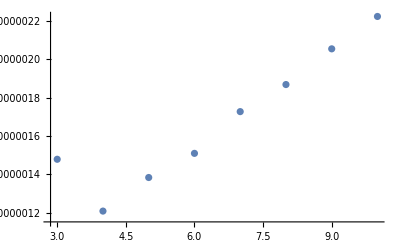

```mathematica
(* Plot results: *)
ListPlot[MapThread[{#1, #2}&, {bandwidthSeq, cvErrors}]]
```

```mathematica
(* Shortcut: *)
bestBandwidth = 4
```

4

```mathematica
bestFits = LoessR[#, bestBandwidth, #[[All, 1]]]&/@bubblesScaled;
```

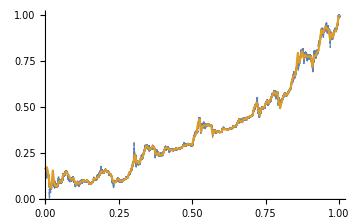
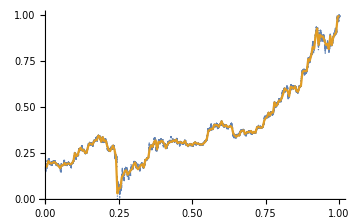

```mathematica
Show[ListPlot[#, ImageSize->Medium],   ListLinePlot[{{{0,0}},Table[{t, LoessR[#, bestBandwidth, t]}, {t, Min[#[[All, 1]]], Max[#[[All, 1]]], .005}]}]]&/@bubblesScaled
```

```mathematica
(* 1.b Detrend: *)
ℛs = Table[bubblesScaled[[i]][[All,2]]-bestFits[[i]], {i, n}]
```

```mathematica
(* 1.c Fit AR(1) error model on the detrended data *)
(* Model the residuals with an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Models=FindProcessParameters[#,ar1Process]&/@ℛs
```

{{ρ→-0.174263,σ→-0.000769467,μ→3.47043×10^-6},{ρ→-0.200438,σ→-0.00133687,μ→-8.12166×10^-6}}

```mathematica
(*Compute the log-likelihood of the fit*)
estimatedProcesses=ar1Process/.#&/@estimatedAR1Models
```

{ARProcess[3.47043×10^-6,{-0.174263},5.9208×10^-7],ARProcess[-8.12166×10^-6,{-0.200438},1.78722×10^-6]}

```mathematica
logLikelihoods=Table[LogLikelihood[estimatedProcesses[[i]],ℛs[[i]]], {i, Length[bubbles]}]
```

{140310.,55629.}

```mathematica
(* Step 2: Characterize error variance. *)
```

```mathematica
(* 2.a Bootstrap the residuals from step 1 and feed them through the fitted AR(1) to simulate errors. *)
(* Allowing for the distribution of the residual standard error on different window sizes to be approximated by Monte Carlo. *)
nPointss=Length/@ℛs;
nSims=1000;
sims=Table[RandomFunction[estimatedProcesses[[i]],{0,nPointss[[i]]-1},nSims], {i, n}];
```

```mathematica
ℛsPlots=Table[MapThread[{#1,#2}&,{Range[0,nPointss[[i]]-1],ℛs[[i]][[;;nPointss[[i]]]]}], {i, n}];
```

```mathematica
paths=#["Paths"]&/@sims;
```

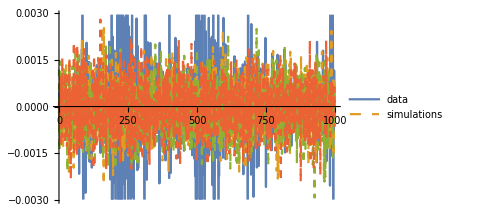
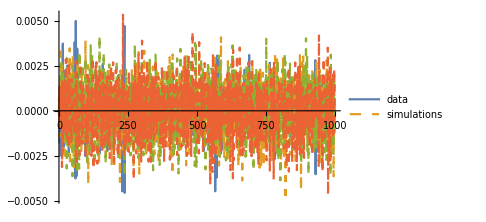

```mathematica
(* Show some simulations and data points *)
showPoints=1000;
showSims=3;
Table[ListLinePlot[Join[{ℛsPlots[[i]][[;;showPoints]]}, paths[[i]][[;;showSims,;;showPoints]]],PlotStyle->{Thick, Dashed, Dashed, Dashed},PlotLegends->{"data","simulations"}, ImageSize->Medium],{i,n}]
```

```mathematica
(* Characterize error variance *)
(* The mean variance of the errors: *)
Variance/@ℛs
```

{6.10648×10^-7,1.8622×10^-6}

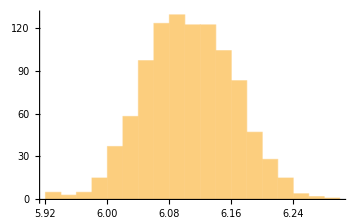
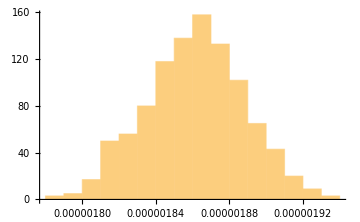

```mathematica
varianceErrors=Table[Map[Variance[#[[All,2]]]&,paths[[i]]], {i, n}];
Histogram[#, ImageSize->Medium]&/@varianceErrors
```

```mathematica
(* The mean variance of the (simulated) residual errors matches the variance of the residuals. *)
Mean/@varianceErrors
```

{6.1054×10^-7,1.8613×10^-6}

```mathematica
(* It matches the found AR1 process model parameter as well: *)
estimatedAR1Models
Map[#^2&,#[[2]]]&/@estimatedAR1Models
```

{{ρ→-0.174263,σ→-0.000769467,μ→3.47043×10^-6},{ρ→-0.200438,σ→-0.00133687,μ→-8.12166×10^-6}}

{σ^2→5.9208×10^-7,σ^2→1.78722×10^-6}

```mathematica
acceptSds =Table[Max[{Variance[ℛs[[i]]],Mean[varianceErrors[[i]]], Map[#^2&,estimatedAR1Models[[i]][[2]]][[2]]}]//Sqrt, {i, n}]
```

{0.00078144,0.00136462}

```mathematica
(* 3. Fit LPPLS function: *)
tc=.
lpplsModel=a +(tc-ti)^m(b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Profiling over 0.1 < m < 0.5, 7 < ω < 11 and 1. < tc < 1.2 *)
(* Try to estimate all the params (using log-likelihood): *)
```

```mathematica
(* TODO: Add ϕ error estimation (AR(1)) param *)
```

```mathematica
(* Uses Normal distribution for the residuals (Slow) *)
numParams =7;(* {a, b, c, d, tc, m, ω} *)
(* Build AR(1) process over the residuals, and compute its Log-Likelihood. Compare AR(1) params and LL with the baseline. *)
```

```mathematica
(* Use the first bubble: *)
bubble
bubbleScaled=bubblesScaled[[bubble]];
```

1

```mathematica
fits=Table[m=.;tc=.;
bestFit=MaximalBy[Flatten[Table[{tc,m,ω,nlm=NonlinearModelFit[Select[bubbleScaled,#[[1]]>= t1&],lpplsModel,{a,b,c,d}, ti];nlm["BestFitParameters"],
ℛ=nlm["FitResiduals"];
(* Fit an AR(1) process *)
ar1Process=ARProcess[μ,{ρ},σ^2];
estimatedAR1Model=FindProcessParameters[ℛ,ar1Process],
LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]},{m,0.1,0.5,1./10}, {ω,8.,14.,1./10},  {tc, bubbleScaled[[-1]][[1]]+0.0001, 1.2,1./50}],2], Last]//Flatten[#, 1]&;modelParams=Join[bestFit[[4]], {Subscript[T, 1]-> t1,tc-> bestFit[[1]],m-> bestFit[[2]], ω-> bestFit[[3]], LL-> bestFit[[6]]},bestFit[[5]]], {t1, 1/7 1/2Range[0,4 2]}]//AbsoluteTiming
```

{3618.97,{{a→4.28424,b→-4.19078,c→0.00745794,d→0.0220161,T_1→0,tc→1.08292,m→0.1,ω→11.1,LL→121675.,ρ→0.998772,σ→-0.00174801,μ→-4.97966×10^-18},{a→4.56076,b→-4.46848,c→0.0107333,d→0.0157871,T_1→1/14,tc→1.10292,m→0.1,ω→12.3,LL→114957.,ρ→0.999012,σ→-0.00158643,μ→2.66961×10^-18},{a→1.69922,b→-1.64092,c→0.0206082,d→0.0084202,T_1→1/7,tc→1.06292,m→0.3,ω→11.1,LL→105741.,ρ→0.999104,σ→-0.00158203,μ→1.16411×10^-18},{a→2.41584,b→-2.34044,c→0.020414,d→0.00197784,T_1→3/14,tc→1.08292,m→0.2,ω→12.2,LL→96415.3,ρ→0.999086,σ→-0.00163452,μ→4.87699×10^-19},{a→1.35113,b→-1.31794,c→0.00173466,d→0.022473,T_1→2/7,tc→1.04292,m→0.4,ω→9.7,LL→87147.9,ρ→0.999098,σ→-0.0016852,μ→-8.08062×10^-20},{a→2.37731,b→-2.2904,c→-0.028111,d→-0.00874869,T_1→5/14,tc→1.08292,m→0.2,ω→14.,LL→78995.8,ρ→0.998831,σ→-0.00165886,μ→-1.22767×10^-18},{a→4.64908,b→-4.57057,c→0.028201,d→-0.0214381,T_1→3/7,tc→1.10292,m→0.1,ω→13.1,LL→69802.4,ρ→0.998598,σ→-0.00168939,μ→9.84882×10^-19},{a→1.37717,b→-1.44556,c→-0.0213006,d→-0.072354,T_1→1/2,tc→1.08292,m→0.5,ω→13.3,LL→60381.7,ρ→0.998744,σ→-0.00178085,μ→-8.72352×10^-19},{a→1.42368,b→-1.5475,c→-0.0435299,d→-0.0202194,T_1→4/7,tc→1.08292,m→0.5,ω→13.7,LL→51711.4,ρ→0.998344,σ→-0.00179633,μ→1.95254×10^-18}}}

```mathematica
(* Timing in minutes: *)
fits[[1]]/60
```

60.3162

```mathematica
(* Average tc: *)
meanTc=Total[fits[[2]][[All,6]][[All,2]]]/Length[fits[[2]]]
```

1.0807

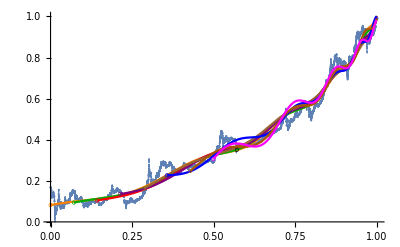

```mathematica
(* Plot of the results: *)
colors={Orange,Darker[Green],Red, Purple, Brown, Blue, Darker[Orange], Magenta,Black};
circles=Table[{colors[[i]],Thickness[0.0012],Circle[{(i-1)/14,lpplsModel/.fits[[2]][[i]]/.ti-> (i-1)/14},{0.005,0.0085}]}, {i, 1,9}];
Show[ListPlot[bubbleScaled, ImageSize->Full, Epilog-> circles], Plot[Table[If[ti>1/14(i-1),Evaluate[lpplsModel/.fits[[2]][[i]]],""], {i, 8}], {ti, 0, 1}, PlotStyle->colors, Evaluated->True]]
```

```mathematica
(* By definition, the best fit is the one with smallest variance: *)
fit=MinimalBy[fits[[2]], (#[[11]][[2]])^2&]//Flatten
```

{a→1.69922,b→-1.64092,c→0.0206082,d→0.0084202,T_1→1/7,tc→1.06292,m→0.3,ω→11.1,LL→105741.,ρ→0.999104,σ→-0.00158203,μ→1.16411×10^-18}

```mathematica
(* Estimate tc 95% CI by Profile Likelihood *)
m=.
ω=.
tc=.
```

```mathematica
(* First do lower leg (most useful one) of the tc CI: *)
(* Slowly reduce tc until the log-likelihood test is 1.92 points below the maximum LL.
First version: Re-fit the linear parameters, keeping the non-linear ones fixed: *)
bestm=m/.fit
bestω=ω/.fit
bestTc=tc/.fit
bestLL=LL/.fit
```

0.3

11.1

1.06292

105741.

```mathematica
t1=Subscript[T, 1]/.fit;
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
```

```mathematica
(* Selected best bubble: *)
bubbleBest=Select[bubbleScaled, #[[1]]>= t1&]
```

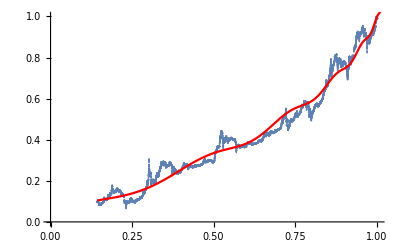

```mathematica
(* Best fit plot *)
Show[ListPlot[bubbleBest, ImageSize->Full], Plot[Evaluate[lpplsModel/.fit], {ti, t1, bestTc}, PlotStyle->{Red}, Evaluated->True]]
```

```mathematica
(* Profile-likelihood-based 95% C.I. for Subscript[t, c]: *)
(* Get nlm function: *)
lpplsModel
```

a+(tc-ti)^m (b+c Cos[ω Log[tc-ti]]+d Sin[ω Log[tc-ti]])

```mathematica
(* Parametrize it: *)
fit
```

{a→1.69922,b→-1.64092,c→0.0206082,d→0.0084202,T_1→1/7,tc→1.06292,m→0.3,ω→11.1,LL→105741.,ρ→0.999104,σ→-0.00158203,μ→1.16411×10^-18}

```mathematica
bestLppls[x_, testTc_:bestTc]:= lpplsModel/.fit[[1;;4]]/.fit[[7;;8]]/.ti-> x/.tc-> testTc
```

```mathematica
mlℛ = Map[#[[2]]-bestLppls[#[[1]]]&, bubbleBest]
```

```mathematica
(* Fit an AR(1) process (Perhaps re-utilize / recompute the non-parametric residuals model, fitted over the selected interval): *)
ar1Process=ARProcess[μ,{ρ},σ^2];
```

```mathematica
estimatedAR1Model=FindProcessParameters[mlℛ,ar1Process]
```

{ρ→0.999104,σ→-0.00158203,μ→1.16411×10^-18}

```mathematica
LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

105741.

```mathematica
bestLL==LogLikelihood[ar1Process/. estimatedAR1Model,mlℛ]
```

True

```mathematica
(* They match! *)
(* Now sligthly vary tc, and recompute residuals: *)
lowCItc=bestTc-10/1326;
ℛ = Map[#[[2]]-bestLppls[#[[1]], lowCItc]&, bubbleBest]
```

```mathematica
lowCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]
```

105739.

```mathematica
bestLL-lowCILL
```

1.92077

```mathematica
{lowCItc, bestTc}
```

{1.05538,1.06292}

```mathematica
(* Fantastic! *)
(* Let's do the upper leg of the CI: *)
highCItc=bestTc+100/14765;
ℛ = Map[#[[2]]-bestLppls[#[[1]], highCItc]&, bubbleBest]
```

```mathematica
highCILL=LogLikelihood[ar1Process/. estimatedAR1Model,ℛ]
```

105739.

```mathematica
bestLL-highCILL
```

1.92017

```mathematica
{lowCItc, bestTc, highCItc}
```

{1.05538,1.06292,1.0697}

```mathematica
(* Now compute the equivalent date of the low CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] lowCItc]
```

Wed 13 Dec 2017 13:05:19

```mathematica
(* Now compute the equivalent date of the high CI tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] highCItc]
```

Thu 28 Dec 2017 03:50:43

```mathematica
(* And the best tc: *)
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] bestTc]
```

Thu 21 Dec 2017 05:53:06

```mathematica
(* This is the date of the actual bubble popping: *)
DatePlus[bubblesDate[[bubble]][[2]], 60]
```

Sun 17 Dec 2017 00:00:00

```mathematica
(* It works! *)
```

```mathematica
(* The mean tc, for reference: *)
meanTc=1.0807015960712094;
DatePlus[bubblesDate[[bubble]][[1]],bubblesDays[[bubble]] meanTc]
```

Mon 8 Jan 2018 09:30:42

```mathematica
(* 2022 / 2023: *)
(* 1. TODO: Load data *)
(* Define range *)
marketCapLogTs2022=Select[marketCapLogTs, UnixTime["2022"]≤ #[[1]]&];
bubbles2022={{"2022-06-18",last}}
```

{{2022-06-18,2022-07-31}}

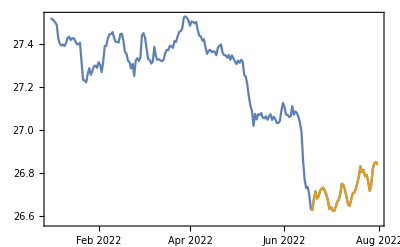

```mathematica
DateListPlot[{marketCapLogTs2022, Select[marketCapLogTs2022,UnixTime[bubbles2022[[1]][[1]]]≤ #[[1]]&]},DateFunction->(FromUnixTime[#]&)]
```

```mathematica
(* Scale data horizontally and vertically: *)
bubble2022Selected=Select[marketCapLogTs2022, UnixTime[bubbles2022[[1]][[1]]]≤ #[[1]]&];
```

```mathematica
bubble2022Scaled= scaleV[scaleH[bubble2022Selected]];
```